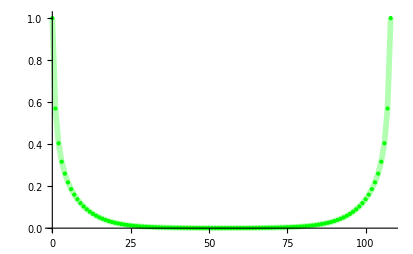

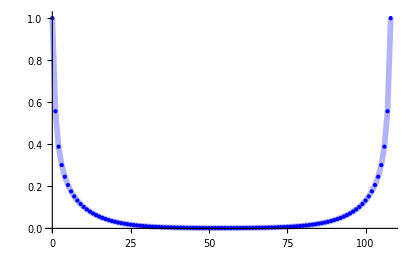

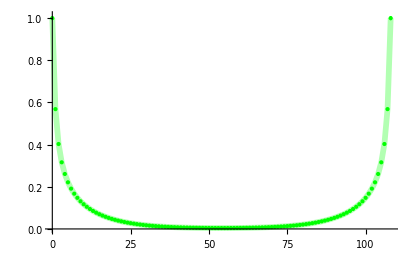

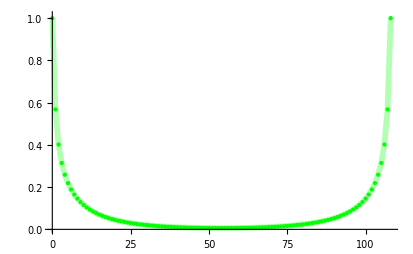

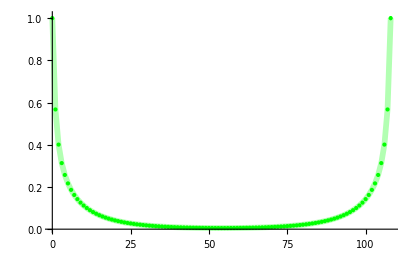

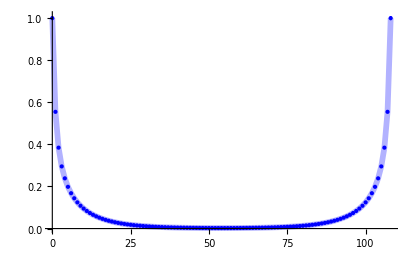

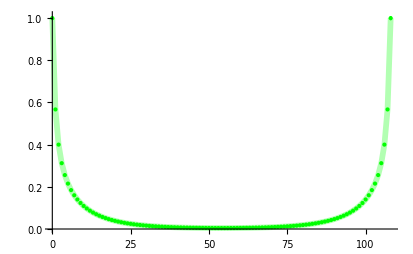

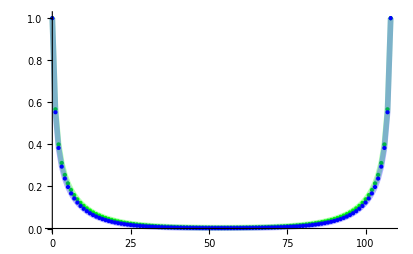

```mathematica
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
N6Data=Import["G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\N6_normal_L108_correlator.txt","Table"];
N9Data=Import["G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\N9_normal_L108_correlator.txt","Table"];
MCLTS=DeleteDuplicates[Join[Transpose[N6Data][[1]],Transpose[N9Data][[1]]]];
MCLTS=Sort[MCLTS];
N6Data=Partition[N6Data,108];
N9Data=Partition[N9Data,108];
MCCorrelatorPlots=Table[{},{LT,MCLTS}];
GeneratePlots[data_,color_]:=Module[{MyData,Gr1,Gr2,LT,ilt},
For[it=1,it≤Length[data],it++,
LT=data[[it]][[1,1]];
ilt=Position[MCLTS,LT][[1,1]];
MyData=Drop[data[[it]],0,1];
PrependTo[MyData,{0,1,0}];
Gr1=PlotWithErrorsTranspose[MyData,PlotRange->All,PlotStyle->{color}];
Gr2=ListPlot[Drop[MyData,0,-1 ],PlotRange->All,Joined->True,PlotStyle->{color,Opacity[0.3],Thickness[0.01]}];
AppendTo[MCCorrelatorPlots[[ilt]],Gr2];
AppendTo[MCCorrelatorPlots[[ilt]],Gr1];
];
];
GeneratePlots[N6Data,Green];
GeneratePlots[N9Data,Blue];
For[i=1,i≤Length[MCCorrelatorPlots],i++,
Print[Show[MCCorrelatorPlots[[i]]]];
];
```